```mathematica
Clear["Global`*"]
```

{1/2,1/2-x+x^2,1/2-x+x^2,1/2-x+2 x^3-x^4,1/2-x+2 x^3-x^4,1/2-x+5 x^4-6 x^5+2 x^6,1/2-x+5 x^4-6 x^5+2 x^6,1/2-x+14 x^5-28 x^6+20 x^7-5 x^8,1/2-x+14 x^5-28 x^6+20 x^7-5 x^8,1/2-x+42 x^6-120 x^7+135 x^8-70 x^9+14 x^10}

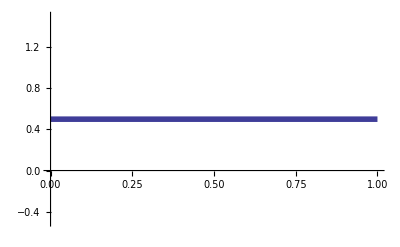
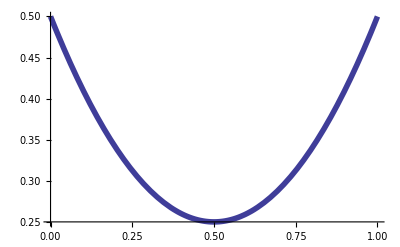
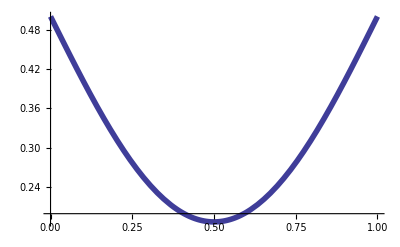
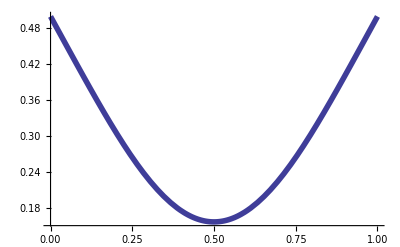
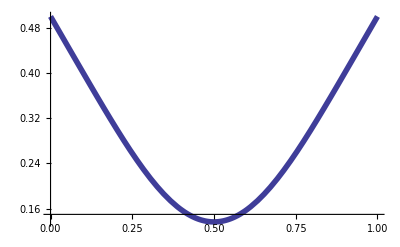
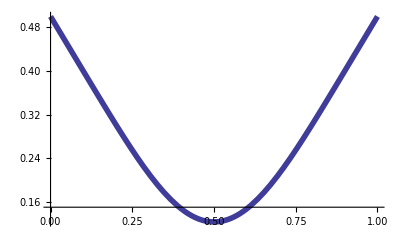
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

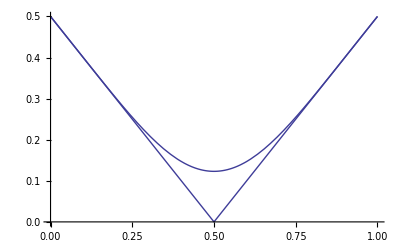

```mathematica
f[y_] = Abs[y-1/2];
P[x_,n_]:= Sum[Binomial[n,p] f[p/n]x^p (1-x)^(n-p),{p,0,n}]
Table[Expand[P[x,k]],{k,1,10}]
Table[Plot[Expand[P[x,k]],{x,0,1},PlotRange->All,PlotStyle->{Thickness[0.01]}],{k,1,10}]
Show[Plot[f[x],{x,0,1}],Plot[P[x,10],{x,0,1}]]
```